# Point Force Greens Functions

```mathematica
r = Sqrt[(x-xs)^2 +(y-ys)^2];
Upt =1/2/Pi*(x-xs)/r^2
s12 = D[Upt,x]
s13 = D[Upt,y]
```

(x-xs)/(2 π ((x-xs)^2+(y-ys)^2))

-(x-xs)^2/(π ((x-xs)^2+(y-ys)^2)^2)+1/(2 π ((x-xs)^2+(y-ys)^2))

-((x-xs) (y-ys))/(π ((x-xs)^2+(y-ys)^2)^2)

## Indefinite integration over a fault defined from y in [-W,W]

```mathematica
Uf = Integrate[Upt,ys,GeneratedParameters->C]
```

-ArcTan[(y-ys)/(x-xs)]/(2 π)+C[1]

## Evaluate limits of integral

```mathematica
U1d =ReplaceAll[Uf,{ys->w,xs->0}]-ReplaceAll[Uf,{ys->-w,xs->0}]//FullSimplify
(*U1d = 1/2/Pi*ArcTan[x^2+y^2-w^2,2*w*x]*)
```

(ArcTan[(w-y)/x]+ArcTan[(w+y)/x])/(2 π)

# Plot displacement field

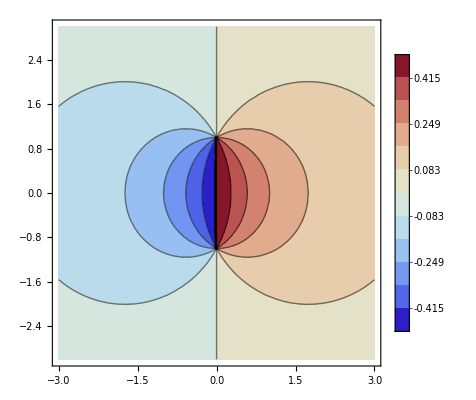

```mathematica
ContourPlot[ReplaceAll[U1d,{w->1}],{x,-3,3},{y,-3,3},ColorFunction->"ThermometerColors",PlotLegends->BarLegend[{Automatic,{-0.5,0.5}}],PlotPoints->20,Contours->11,PlotRange->{-0.5,0.5}]
```

-(w (w^2+x^2-y^2))/(π (x^2+(w-y)^2) (x^2+(w+y)^2))

-(2 w x y)/(π (x^2+(w-y)^2) (x^2+(w+y)^2))

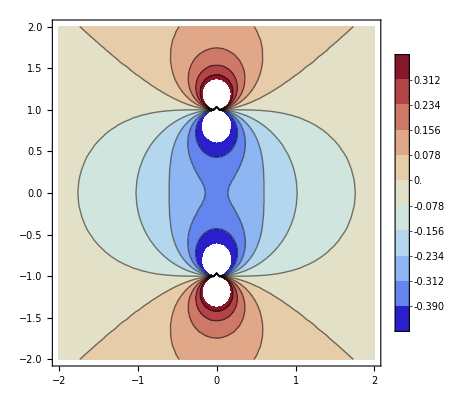

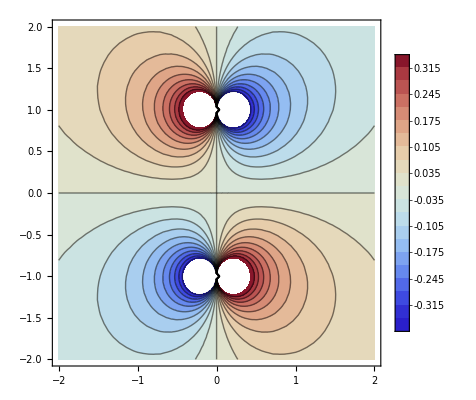

```mathematica
S12 = D[U1d,x]//FullSimplify
S13 = D[U1d,y]//FullSimplify
ContourPlot[ReplaceAll[S12,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,Contours->10]
ContourPlot[ReplaceAll[S13,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,Contours->20]
```

# Integrate point source with linear slip

```mathematica
Ulin = Integrate[Upt*(a0+a1*ys),ys,GeneratedParameters->C]
```

C[1]+((x-xs) (-((a0+a1 y) ArcTan[(y-ys)/(x-xs)])/(x-xs)+1/2 a1 Log[x^2-2 x xs+xs^2+(y-ys)^2]))/(2 π)

## Insert limits of integration

```mathematica
Ulin1d =ReplaceAll[Ulin,{ys->w,xs->0}]-ReplaceAll[Ulin,{ys->-w,xs->0}]//FullSimplify
```

(2 (a0+a1 y) ArcTan[(w-y)/x]+2 (a0+a1 y) ArcTan[(w+y)/x]+a1 x (Log[x^2+(w-y)^2]-Log[x^2+(w+y)^2]))/(4 π)

## Plot displacement and stress fields

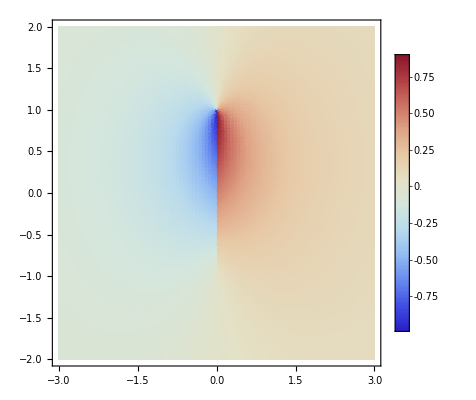

```mathematica
DensityPlot[ReplaceAll[Ulin1d,{w->1,a0->1,a1->1}],{x,-3,3},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->Full,PlotPoints->100,ScalingFunctions->{"Linear","Linear"}]
```

((4 w (-a0 (w^2+x^2-y^2)+a1 y (-w^2+x^2+y^2)))/(w^4+2 w^2 (x-y) (x+y)+(x^2+y^2)^2)+a1 Log[x^2+(w-y)^2]-a1 Log[x^2+(w+y)^2])/(4 π)

(-(4 w x (2 a0 y+a1 (w^2+x^2+y^2)))/(w^4+2 w^2 (x-y) (x+y)+(x^2+y^2)^2)+2 a1 (ArcTan[(w-y)/x]+ArcTan[(w+y)/x]))/(4 π)

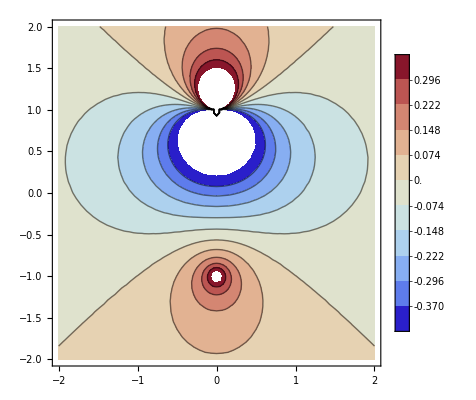

-Graphics-

```mathematica
S12 = D[Ulin1d,x]//FullSimplify
S13 = D[Ulin1d,y]//FullSimplify
ContourPlot[ReplaceAll[S12,{w->1,a0->1,a1->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,Contours->10]
ContourPlot[ReplaceAll[S13,{w->1,a0->1,a1->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,Contours->10,PlotPoints->100]
```

# Integrate point source with quadratic slip

```mathematica
Uquad = Integrate[Upt*(Subscript[α, 0]+Subscript[α, 1]*ys+Subscript[α, 2]*ys^2),ys,GeneratedParameters->C]
```

C[1]+((x-xs) ((-y+ys) α_2+1/2 Log[x^2-2 x xs+xs^2+(y-ys)^2] (α_1+2 y α_2)-(ArcTan[(y-ys)/(x-xs)] (α_0+y α_1-(x^2-2 x xs+xs^2-y^2) α_2))/(x-xs)))/(2 π)

## Insert limits of integration

```mathematica
Uquad1d =ReplaceAll[Uquad,{ys->w,xs->0}]-ReplaceAll[Uquad,{ys->-w,xs->0}]//FullSimplify
```

1/(2 π)x ((w-y) α_2+(w+y) α_2+1/2 Log[x^2+(w-y)^2] (α_1+2 y α_2)-1/2 Log[x^2+(w+y)^2] (α_1+2 y α_2)+(ArcTan[(w-y)/x] (α_0+y α_1+(-x+y) (x+y) α_2))/x+(ArcTan[(w+y)/x] (α_0+y α_1+(-x+y) (x+y) α_2))/x)

## Plot displacement field

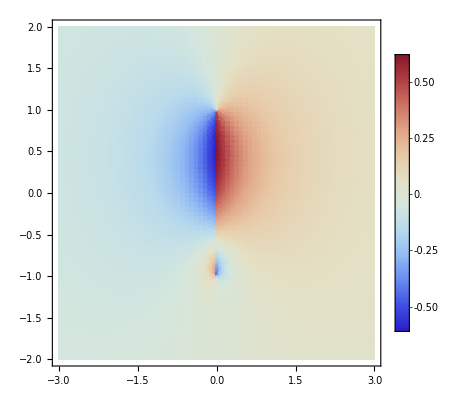

```mathematica
DensityPlot[ReplaceAll[Uquad1d,{w->1,Subscript[α, 0]->1,Subscript[α, 1]->1,Subscript[α, 2]->-1}],{x,-3,3},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->Full,PlotPoints->71,ScalingFunctions->{"Linear","Linear"}]
```